```mathematica
E1=4000;
```

```mathematica
ratio[A2_,E2_]=A2/A1*Exp[-E2/T]/Exp[-E1/T]
```

(A2 ⅇ^(4000/T-E2/T))/A1

```mathematica
fcn1[T_]=ratio[A1,.5*E1]
```

ⅇ^(2000./T)

```mathematica
fcn2[T_]=ratio[.25A1,1E1]
```

0.25

```mathematica
fcn3[T_]=ratio[.25A1,.5E1]
```

0.25 ⅇ^(2000./T)

```mathematica
fcn4[T_]=ratio[10A1,.5E1]
```

10 ⅇ^(2000./T)

```mathematica
fcn5[T_]=ratio[A1,.75E1]
```

ⅇ^(1000./T)

```mathematica
fcn6[T_]=ratio[.5A1,1E1]
```

0.5

```mathematica
fcn7[T_]=ratio[.5A1,2E1]
```

0.5 ⅇ^(-4000/T)

```mathematica
fcn8[T_]=ratio[2A1,2E1]
```

2 ⅇ^(-4000/T)

```mathematica
fcn9[T_]=ratio[2A1,10E1]
```

2 ⅇ^(-36000/T)

```mathematica
TableForm[Table[ratio[n*A1,k*E1],{n,.5,4},{k,.5,4}],TableHeadings->{{"A2=A1/2","A2=3A1/2","A2=5A1/2","A2=7A1/2"},{"E2=E1/2","E2=3E1/2","E2=5E1/2","E2=7E1/2"}}]
```

| E2=E1/2 | E2=3E1/2 | E2=5E1/2 | E2=7E1/2
A2=A1/2 | 0.5 ⅇ^(2000./T) | 0.5 ⅇ^(-2000./T) | 0.5 ⅇ^(-6000./T) | 0.5 ⅇ^(-10000./T)
A2=3A1/2 | 1.5 ⅇ^(2000./T) | 1.5 ⅇ^(-2000./T) | 1.5 ⅇ^(-6000./T) | 1.5 ⅇ^(-10000./T)
A2=5A1/2 | 2.5 ⅇ^(2000./T) | 2.5 ⅇ^(-2000./T) | 2.5 ⅇ^(-6000./T) | 2.5 ⅇ^(-10000./T)
A2=7A1/2 | 3.5 ⅇ^(2000./T) | 3.5 ⅇ^(-2000./T) | 3.5 ⅇ^(-6000./T) | 3.5 ⅇ^(-10000./T)

```mathematica
TableForm[Table[ratio[n*A1,k*E1],{n,.5,4},{k,.5,2}],TableHeadings->{{"A2=A1/2","A2=3A1/2","A2=5A1/2","A2=7A1/2"},{"E2=E1/2","E2=3E1/2","E2=5E1/2","E2=7E1/2"}}]
```

| E2=E1/2 | E2=3E1/2
A2=A1/2 | 0.5 ⅇ^(2000./T) | 0.5 ⅇ^(-2000./T)
A2=3A1/2 | 1.5 ⅇ^(2000./T) | 1.5 ⅇ^(-2000./T)
A2=5A1/2 | 2.5 ⅇ^(2000./T) | 2.5 ⅇ^(-2000./T)
A2=7A1/2 | 3.5 ⅇ^(2000./T) | 3.5 ⅇ^(-2000./T)

```mathematica
TableForm[Table[ratio[n*A1,k*E1],{n,.5,4},{k,2,3}],TableHeadings->{{"A2=A1/2","A2=3A1/2","A2=5A1/2","A2=7A1/2"},{"E2=5E1/2","E2=7E1/2"}}]
```

| E2=5E1/2 | E2=7E1/2
A2=A1/2 | 0.5 ⅇ^(-4000/T) | 0.5 ⅇ^(-8000/T)
A2=3A1/2 | 1.5 ⅇ^(-4000/T) | 1.5 ⅇ^(-8000/T)
A2=5A1/2 | 2.5 ⅇ^(-4000/T) | 2.5 ⅇ^(-8000/T)
A2=7A1/2 | 3.5 ⅇ^(-4000/T) | 3.5 ⅇ^(-8000/T)

Table::itform: Argument TableHeadings → {"n", "k"} at position 4 does not have the correct form for an iterator.

Table[ratio[n,k],{n,0.5,5},{k,0.5,5},TableHeadings→{n,k}]

```mathematica
LogLinear
```

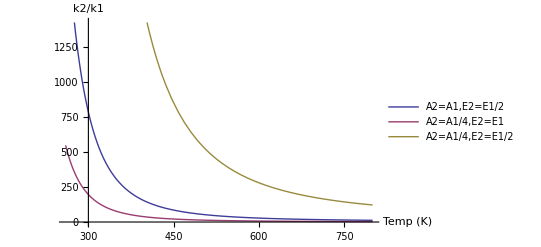

```mathematica
Plot[{fcn1[T],fcn3[T],fcn4[T]},{T,260,800},PlotRange->Automatic,AxesLabel->{"Temp (K)","k2/k1"},PlotLegends->{"A2=A1,E2=E1/2","A2=A1/4,E2=E1/2","A2=10*A1,E2=E1/2","A2=A1,E2=E1*3/4","A2=A1/2,E2=E1"}]
```

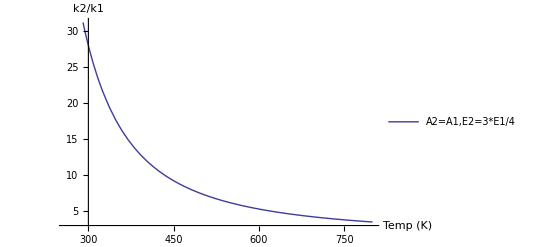

```mathematica
Plot[{fcn5[T]},{T,260,800},PlotRange->Automatic,AxesLabel->{"Temp (K)","k2/k1"},AxesLabel->{"Temp (K)","k2/k1"},PlotLegends->{"A2=A1,E2=3*E1/4"}]
```

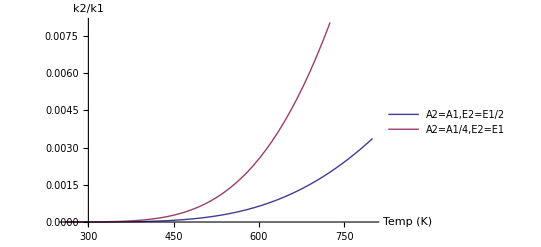

```mathematica
Plot[{fcn7[T],fcn8[T]},{T,260,800},PlotRange->Automatic,AxesLabel->{"Temp (K)","k2/k1"},PlotLegends->{"A2=A1,E2=E1/2","A2=A1/4,E2=E1","A2=A1/4,E2=E1/2","A2=10*A1,E2=E1/2","A2=A1,E2=E1*3/4","A2=A1/2,E2=E1"}]
```

```mathematica
fcn9[T]
```